Coded by Manish J. Thapa under supervision of Dr. Johannes Heinsoo @Quantum Device Lab, ETH Zurich, April 2016

# Simulations of CPHASE Gate for Quantum Processor

```mathematica
Plot[Piecewise[{{-0.265*HannWindow[(x-38)/60],66>x>0},{0,80>x>55},{0.256*HannWindow[(x-126)/65],157>x>80}}],{x,0,200}]
```

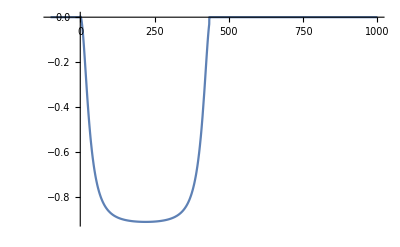

```mathematica
Plot[Piecewise[{{-1.-0.1/ArcTan[1Cos[ (x/L)]-1.1],6.2L>x>0},{0,x>L}}]/.{L->70},{x,-100,1000},PlotRange->All]
```

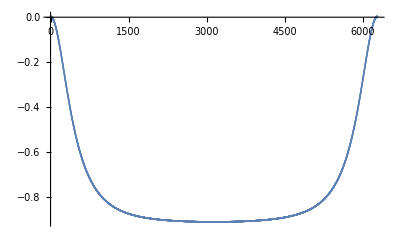

```mathematica
ListPlot[Table[-1-0.1/ArcTan[Cos[1.x/1]-1.1],{x,0,2.Pi,0.001}],PlotRange->All]
```

## def

```mathematica
Unprotect[CircleDot];
CircleDot=KroneckerProduct;
Protect[CircleDot];
```

```mathematica
Unprotect[Plus];
```

```mathematica
Symbolize[Subscript[H, _]];
```

```mathematica
id3=IdentityMatrix[3];
```

```mathematica
ge={0,1,0,0,0,0,0,0,0};
eg={0,0,0,1,0,0,0,0,0};
ee={0,0,0,0,1,0,0,0,0};
ef={0,0,0,0,0,1,0,0,0};
fg={0,0,0,0,0,0,1,0,0};
fe={0,0,0,0,0,0,0,1,0};
ff={0,0,0,0,0,0,0,0,1};
```

```mathematica
gf={0,0,1,0,0,0,0,0,0};
```

```mathematica
gg={1,0,0,0,0,0,0,0,0};
```

```mathematica
Subscript[H, a1]=h ({{0, 0, 0}, {0, wa1, 0}, {0, 0, wa2}})⊙id3;
```

```mathematica
Subscript[H, b1]=h id3⊙({{0, 0, 0}, {0, wb1, 0}, {0, 0, wb2}});
```

```mathematica
Subscript[H, Jab1]=({{0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, √2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, √2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0}});
```

```mathematica
Subscript[H, rwa1]=h IdentityMatrix[9]rwa;
```

```mathematica
gaussian[σ_]:=PDF[NormalDistribution[0,σ],t];
```

```mathematica
pulse=Simplify[Convolve[δ UnitBox[(t-offset)/(len)],gaussian[σ],t,t2],Assumptions->{len>0}];
```

```mathematica
fpulseparams={offset->52+3σ,σ->1.7857,t2->t};
```

```mathematica
(*before {offset->36+3σ,σ->7.1428,t2->t} total time=100*)
```

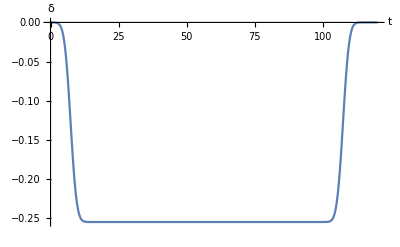

```mathematica
Plot[pulse//.fpulseparams/.{δ->-0.255,len->100},{t,0,120},AxesLabel->{t,δ},PlotRange->All]
```

```mathematica
fpulse[t_,δ_,len_]:=pulse//.fpulseparams;
```

```mathematica
params={
wa1->5.37243+fpulse[t,δ,len],
wa2->2*wa1-α,
wb1->4.81672,
wb2->2*wb1-α,
α->0.3,
ℏ->h/(2π),
h->1,
rwa->0 (*-Subscript[ν, b1]*)(*-(Subscript[ν, a1]+Subscript[ν, b1])*),
J->1/(2 √2 60)
};
```

```mathematica
Row[{
(Subscript[H, full1]=Subscript[H, a1]+Subscript[H, b1]+h J Subscript[H, Jab1]+h J Subscript[H, Jab1]†+Subscript[H, rwa1])
}];
```

```mathematica
(Subscript[H, full]=Subscript[H, full1]//.params)//MatrixForm;
```

```mathematica
(Hfull=Subscript[H, a1]+Subscript[H, b1]+h J Subscript[H, Jab1]+h J Subscript[H, Jab1]†+Subscript[H, rwa1]//.params)//MatrixForm;
```

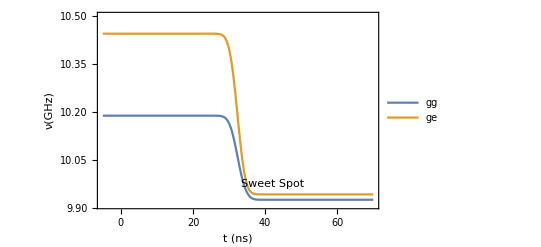

```mathematica
Show[Plot[Evaluate@Eigenvalues[Subscript[H, full]/.{δ->-0.255,len->50}][[8;;9]],{t,-5,70},PlotLegends->Placed[{"|11>","|20>"},PlotRange->{9.91,10.5},Frame->True,FrameLabel->{"t (ns)","ν(GHz)"}],Graphics[Text["Sweet Spot",{42.11,9.974}]]]
```

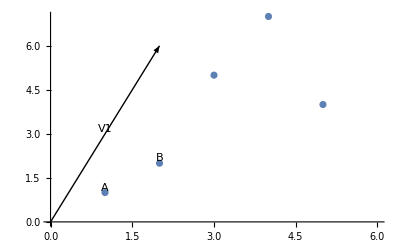

```mathematica
v={1,2,5,7,4};
Show[ListPlot[v,PlotRange->{{0,6},{0,7}}],Graphics[Text["A",{1,1},{0,-1}]],Graphics[Text["B",{2,2},{0,-1}]],Graphics[Arrow[{{0,0},{2,6}}]],Graphics[Text["V1",{1,3},{0,-2}]]]
```

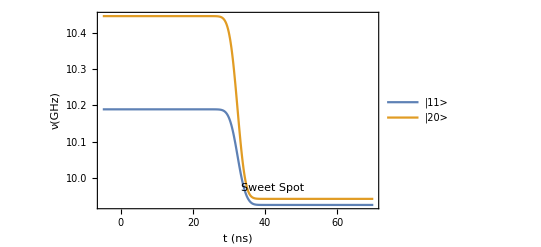

```mathematica
Show[Plot[Evaluate@Eigenvalues[Subscript[H, full]/.{δ->-0.255,len->50}][[8;;9]],{t,-5,70},PlotLegends->Placed[{"|11>","|20>"},Above],Frame->True,FrameLabel->{"t (ns)","ν(GHz)"},LabelStyle->{FontSize->15}],Graphics[Text["Sweet Spot",{42.11,9.974}]]]
```

## solving geometric phase - ND solver

```mathematica
constructU[h_,tinit_,tfinal_,n_]:=Module[{dt=N[(tfinal-tinit)/n],curVal=IdentityMatrix[Length@h[0]]},Do[curVal=MatrixExp[-I*2Pi*h[t]*dt].curVal,{t,tinit,tfinal-dt,dt}];
curVal];
```

```mathematica
Hfunc[tt_,d_,l_]:=Hfull/.{t->tt,δ->d,len->l};
```

```mathematica
pauliX[α_]:=MatrixExp[ⅈ({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}) α/2];
```

```mathematica
pauliY[α_]:=MatrixExp[ⅈ({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 1}}) α/2];
```

```mathematica
EvolX[α_]:=pauliX[α]⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
EvolY[α_]:=pauliY[α]⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
EvolZ=({{-1, 0, 0}, {0, 1, 0}, {0, 0, 1}})⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
dimx[wv_]:=((EvolX[π/2].wv)*.EvolZ.(EvolX[π/2].wv));
```

```mathematica
dimy[wv_]:=((EvolY[π/2].wv)*.EvolZ.(EvolY[π/2].wv));
```

```mathematica
ψ1= {0,1/√2 ,0,0,1/√2 ,0,0,0,0};
```

```mathematica
ψ2={1/√2,0 ,0,1/√2,0 ,0,0,0,0};
```

```mathematica
sol1=First@ParametricNDSolve[{I D[h[t],t]==2 Pi Subscript[H, full].h[t],h[0]==ψ1},h,{t,0,100},{δ,len}];
```

```mathematica
i[δ_,len_]:=h[δ,len][100]/.sol1;
```

```mathematica
sol2=First@ParametricNDSolve[{I D[m[t],t]==2 Pi Subscript[H, full].m[t],m[0]==ψ2},m,{t,0,100},{δ,len}];
```

```mathematica
n[δ_,len_]:=m[δ,len][100]/.sol2;
```

```mathematica
angelDif[α_,β_]:=Module[{dif=α-β},Min[Abs[dif],Abs[dif+2π],Abs[dif-2π]]]
```

```mathematica
phase[δ_,len_]:=angelDif[Arg[dimy[i[δ,len]]+ⅈ dimx[i[δ,len]]],Arg[dimy[n[δ,len]]+ⅈ dimx[n[δ,len]]]];
```

```mathematica
phaseee=Table[phase[δ,len]/Pi 180,{δ,-0.256,-0.256,0.01},{len,60,60,2}]
```

{{176.52}}

## solving dynamic phase

```mathematica
DistributeDefinitions[constructU];
DistributeDefinitions[Hfunc];
DistributeDefinitions[Hfull];
```

```mathematica
id=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
ϕA= {1/√2,0 ,0,1/√2,0,0,0,0,0}; (*(g+e)g*)
```

```mathematica
ϕB={1/√2,1/√2 ,0,0,0,0,0,0,0}; (*g(g+e)*)
```

```mathematica
solving1=First@ParametricNDSolve[{I D[hdyn[t],t]==2 Pi Subscript[H, full].hdyn[t],hdyn[0]==ϕA},hdyn,{t,0,100},{δ,len}];
```

```mathematica
idyn[δ_,len_]:=hdyn[δ,len][100]/.solving1;
```

```mathematica
solving2=First@ParametricNDSolve[{I D[mdyn[t],t]==2 Pi Subscript[H, full].mdyn[t],mdyn[0]==ϕB},mdyn,{t,0,100},{δ,len}];
```

```mathematica
ndyn[δ_,len_]:=mdyn[δ,len][100]/.solving2;
```

```mathematica
pauliXd[α_]:=MatrixExp[ⅈ({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}}) α/2];
```

```mathematica
pauliYd[α_]:=MatrixExp[ⅈ({{0, -ⅈ, 0}, {ⅈ, 0, 0}, {0, 0, 1}}) α/2];
```

```mathematica
EvolX1[α_]:=pauliXd[α]⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
EvolY1[α_]:=pauliYd[α]⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
EvolZ1=({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}})⊙({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
EvolX2[α_]:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})⊙pauliXd[α];
```

```mathematica
EvolY2[α_]:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})⊙pauliYd[α];
```

```mathematica
EvolZ2=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})⊙({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}});
```

```mathematica
dimx1[wv_]:=((EvolX1[π/2].wv)*.EvolZ1.(EvolX1[π/2].wv));
```

```mathematica
dimy1[wv_]:=((EvolY1[π/2].wv)*.EvolZ1.(EvolY1[π/2].wv));
```

```mathematica
dimx2[wv_]:=((EvolX2[π/2].wv)*.EvolZ2.(EvolX2[π/2].wv));
```

```mathematica
dimy2[wv_]:=((EvolY2[π/2].wv)*.EvolZ2.(EvolY2[π/2].wv));
```

```mathematica
ϕ1[δ_,len_]:=Arg[dimy1[idyn[δ,len]]+ⅈ dimx1[idyn[δ,len]]]; (*first qubit*)
```

```mathematica
ϕ2[δ_,len_]:=Arg[dimy2[ndyn[δ,len]]+ⅈ dimx2[ndyn[δ,len]]]; (*second qubit*)
```

## Fidelity

FIND MAXIMUM

```mathematica
wrProb[δ_?NumberQ,len_?NumberQ]:=Abs[ee*.#&@(constructU[Hfunc[#,δ,len]&,0,120,600]).ee]^2;
```

```mathematica
FindMaximum[wrProb[-0.256,len],{len,65}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.999319,{len→62.7052}}

```mathematica
Abs[ee*.#&@(constructU[Hfunc[#,-0.255,61]&,0,120,600]).ee]^2
```

0.9968

```mathematica
P=({{1, 0}, {0, 1}, {0, 0}})⊙({{1, 0}, {0, 1}, {0, 0}});
```

```mathematica
σz[ϕ_]:=MatrixExp[-ⅈ({{1, 0, 0}, {0, -1, 0}, {0, 0, 1}}) ϕ/2];
```

```mathematica
Uideal=DiagonalMatrix[{1,1,1,-1}];
```

```mathematica
Udyn[δ_,len_]:=(Pᵀ.(σz[-ϕ1[δ,len]]⊙σz[-ϕ2[δ,len]]).P);
```

```mathematica
unitaryarray=Table[#&@(constructU[Hfunc[#,δ,len]&,0,120,600]),{δ,-0.265,-0.245,0.00015},{len,0.1,100,1}];
```

$Aborted

```mathematica
Export["zoomedchevronunitary.wdx",unitaryarray];
```

```mathematica
Dimensions[unitaryarray]
```

{2}

```mathematica
Export["unitary_26525000002_58_78_01_3X_wdx",unitaryarray]
```

unitary_26525000002_68_88_01_5x_FINAL.wdx

```mathematica
fid2x=Table[((Abs[Tr[(Uideal†.Pᵀ.unitaryarray[[j,i,All,All]].P).(Pᵀ.(σz[(Arg[dimy1[unitaryarray[[j,i,All,All]].ϕA]+ⅈ dimx1[unitaryarray[[j,i,All,All]].ϕA]])]⊙σz[(Arg[dimy2[unitaryarray[[j,i,All,All]].ϕB]+ⅈ dimx2[unitaryarray[[j,i,All,All]].ϕB]])]).P)]]^2)+Tr[Uideal†.Uideal])/20,{j,Range[301]},{i,Range[21]}];
```

```mathematica
Export["fid_26525000002_58_78_01_3X_FINAL.dat",fid2x]
```

fid_26525000002_53_73_01_x_FINAL.dat

```mathematica
pop2xx=Table[Abs[ee*.unitaryarray[[j,i,All,All]].ee]^2,{j,Range[301]},{i,Range[21]}];
```

```mathematica
Unprotect[Times]
```

{Times}

```mathematica
importedunitary=Import["unitary_26525000002_68_88_01_5x_FINAL.wdx"];
```

$Aborted

```mathematica
fgi=Table[angelDif[Arg[dimy[unitaryarray[[j,i,All,All]].ψ1]+ⅈ dimx[unitaryarray[[j,i,All,All]].ψ1]],Arg[dimy[unitaryarray[[j,i,All,All]].ψ2]+ⅈ dimx[unitaryarray[[j,i,All,All]].ψ2]]]/Pi 180,{j,Range[301]},{i,Range[21]}];
```

```mathematica
Export["phase_26525000002_53_73_01_x_FINAL.dat",fgi]
```

phase_26525000002_53_73_01_x_FINAL.dat

```mathematica
ListContourPlot[fid2x,Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,All},DataRange->{{58,78},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"fidelity",InterpolationOrder->1,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]
```

```mathematica
impphase=Import["phase_26525000002_53_73_01_x_FINAL.dat"];
```

NEW ROUGH

```mathematica
impunit=Import["unitary_26525000002_68_88_01_5x_FINAL.wdx"];
```

```mathematica
popNew=Table[Abs[ee*.impunit[[j,i,All,All]].ee]^2,{j,Range[301]},{i,Range[21]}];
```

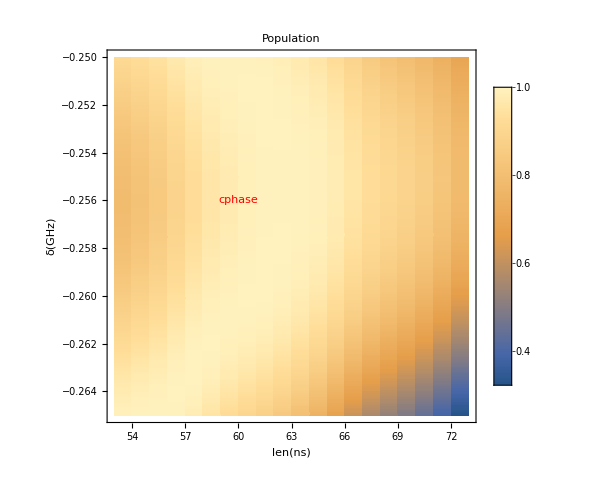

```mathematica
ListDensityPlot[popNew,Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Population",InterpolationOrder->0,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]
```

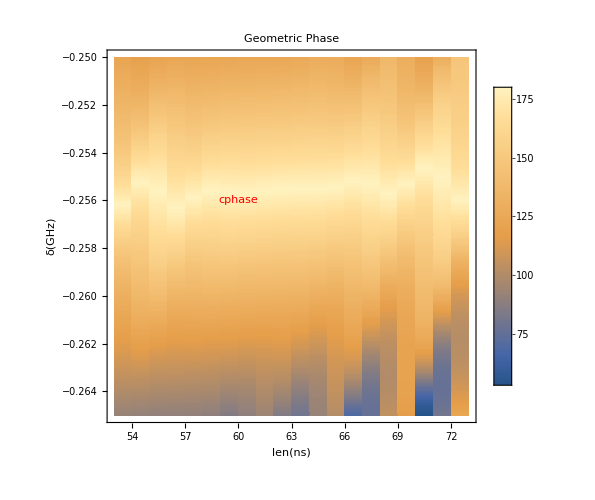

```mathematica
ListDensityPlot[impphase,Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Geometric Phase",InterpolationOrder->0,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]
```

```mathematica
ListContourPlot[Import["fid_26525000002_53_73_01_x_FINAL.dat"],Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"fidelity",InterpolationOrder->1,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]
```

-Graphics-

```mathematica
(*Contours->{{0.99,{Thick,Dashed,Black}},{0.998,{Thick,Dashed,Black}},{0.65,{Thick,Dashed,Black}}}*)
```

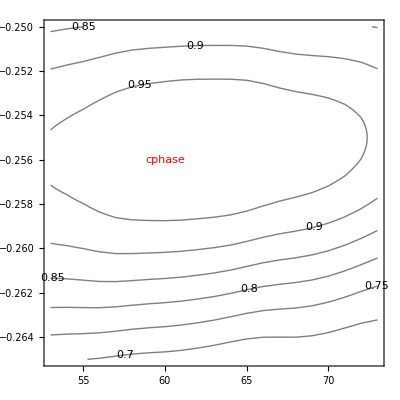

```mathematica
ListContourPlot[Import["fid_26525000002_53_73_01_x_FINAL.dat"],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]
```

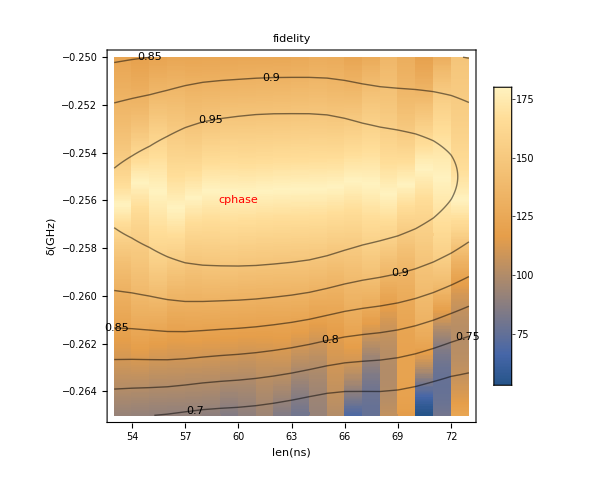

```mathematica
Show[ListDensityPlot[impphase,Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"fidelity",InterpolationOrder->0,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}],ListContourPlot[Import["fid_26525000002_53_73_01_x_FINAL.dat"],PlotRange->{All,All,All},DataRange->{{53,73},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Epilog->{Text[Style[TraditionalForm[cphase],Red],{60,-0.256}]}]]
```

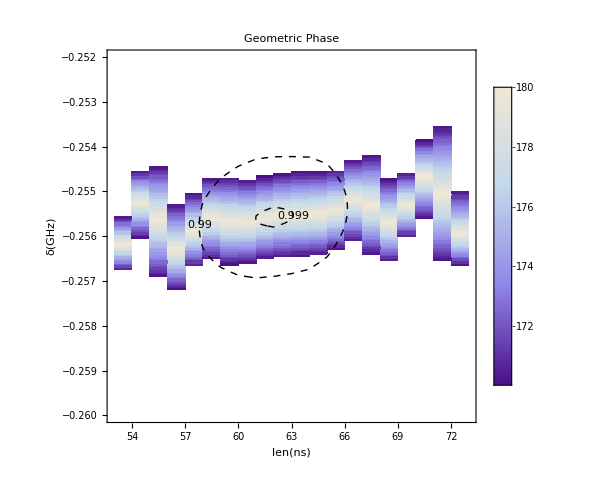

```mathematica
Show[ListDensityPlot[impphase,Mesh->None,ColorFunction->"LakeColors",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,{-0.260,-0.252},{170,180}},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Geometric Phase",InterpolationOrder->0],ListContourPlot[Import["fid_26525000002_53_73_01_x_FINAL.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{53,73},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.99,{Thick,Dashed,Black}},{0.999,{Thick,Dashed,Black}},{0.65,{Thick,Dashed,Black}}}]]
```

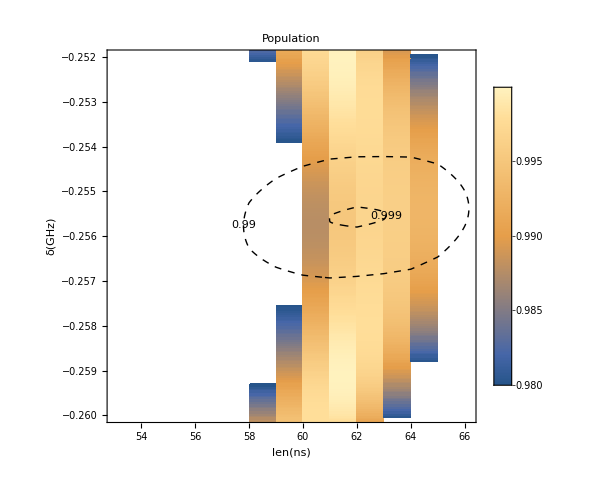

```mathematica
Show[ListDensityPlot[popNew,Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,{-0.260,-0.252},{0.98,1}},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Population",InterpolationOrder->0],ListContourPlot[Import["fid_26525000002_53_73_01_x_FINAL.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{53,73},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.99,{Thick,Dashed,Black}},{0.999,{Thick,Dashed,Black}},{0.65,{Thick,Dashed,Black}}}]]
```

Hanning Window

```mathematica
Plot[5-HannWindow[x-4,10],{x,-10,10}]
```

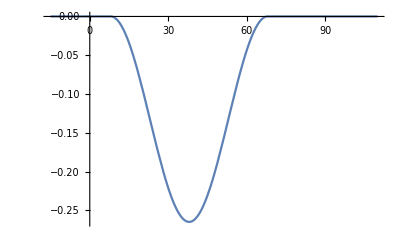

```mathematica
Plot[-0.265*HannWindow[(x-38)/60,1/2],{x,-15,110}]
```

HIGH RESOLUTION

```mathematica
Directory[]
```

D:\Users\Manish\Documents

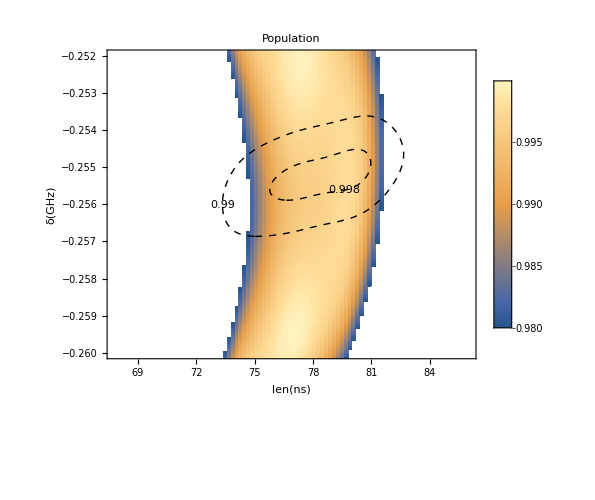

```mathematica
Show[ListDensityPlot[Import["new_pop_26525000002_66_86_02_4x.dat"],Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{All,{-0.260,-0.252},{0.98,1}},DataRange->{{66,86},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Population",InterpolationOrder->0],ListContourPlot[Import["new_fid_26525000002_66_86_02_4x.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{66,86},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.99,{Thick,Dashed,Black}},{0.998,{Thick,Dashed,Black}},{0.65,{Thick,Dashed,Black}}}]]
```

```mathematica
realunitary=Import["new_unitary_26525000002_53_73_02_2x.wdx"];
```

```mathematica
relphase=Table[angelDif[Arg[dimy[realunitary[[j,i,All,All]].ψ1]+ⅈ dimx[realunitary[[j,i,All,All]].ψ1]],Arg[dimy[realunitary[[j,i,All,All]].ψ2]+ⅈ dimx[realunitary[[j,i,All,All]].ψ2]]]/Pi 180,{j,Range[751]},{i,Range[101]}];
```

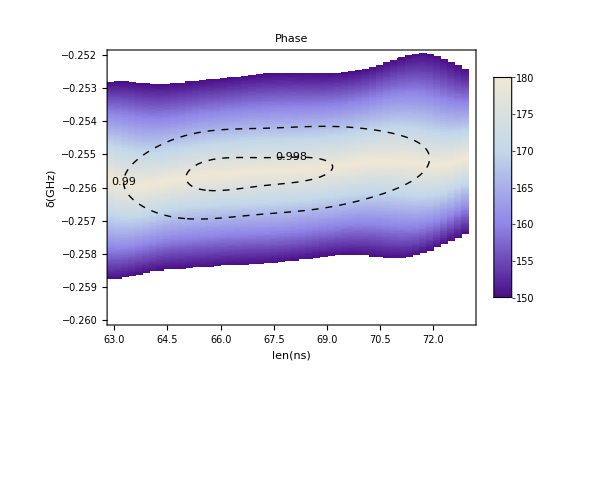

```mathematica
Show[ListDensityPlot[relphase,ColorFunction->"LakeColors",Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{{63,73},{-0.260,-0.252},{150,180}},DataRange->{{53,73},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},RotateLabel->False,LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"Phase",InterpolationOrder->0],ListContourPlot[Import["new_fid_26525000002_53_73_02_2x.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{53,73},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.99,{Thick,Dashed,Black}},{0.998,{Thick,Dashed,Black}},{0.65,{Thick,Dashed,Black}}}]]
```

```mathematica
Directory[]
```

D:\Users\Manish\Documents

```mathematica
uni=Import["new_unitary_26525000002_53_73_02_x.wdx"];
```

```mathematica
uni2=Import["new_unitary_26525000002_53_73_02_2x.wdx"];
```

```mathematica
uni3=Import["new_unitary_26525000002_59_79_02_3x.wdx"];
```

```mathematica
RPhase3=Table[angelDif[Arg[dimy[uni3[[j,i,All,All]].ψ1]+ⅈ dimx[uni3[[j,i,All,All]].ψ1]],Arg[dimy[uni3[[j,i,All,All]].ψ2]+ⅈ dimx[uni3[[j,i,All,All]].ψ2]]]/Pi 180,{j,Range[751]},{i,Range[101]}];
```

```mathematica
Export["rphase3x.dat",RPhase3];
```

```mathematica
Table[Abs[ee*.uni[[j,i,All,All]].ee]^2,{j,Range[1]},{i,Range[2]}]
```

{{0.992468,0.993667}}

```mathematica
Dimensions[uni]
```

{751,101,9,9}

```mathematica
colorscheme=Table[Blend[{Red,White,Blue},i^2],{i,0,1,0.1}];
```

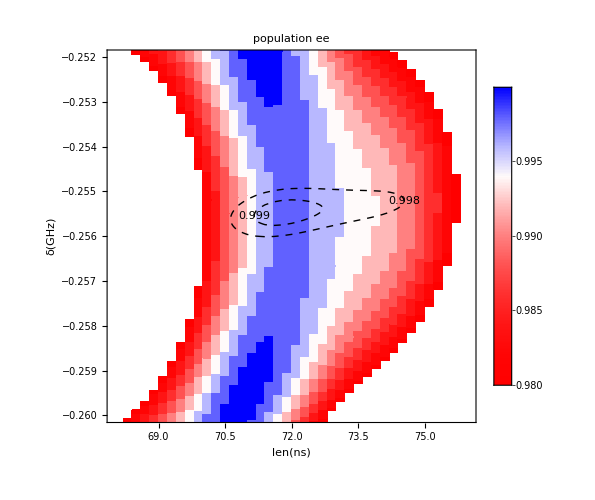

```mathematica
Show[ListDensityPlot[Table[Abs[ee*.uni3[[j,i,All,All]].ee]^2,{j,Range[751]},{i,Range[101]}],Mesh->None,ColorFunction->colorscheme,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{{68,76},{-0.260,-0.252},{0.98,1}},DataRange->{{59,79},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"population ee",InterpolationOrder->0],ListContourPlot[Import["new_fid_26525000002_59_79_02_3x.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{59,79},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.998,{Thick,Dashed,Black}},{0.999,{Thick,Dashed,Black}}}]]
```

```mathematica
RPhase2=Table[angelDif[Arg[dimy[uni2[[j,i,All,All]].ψ1]+ⅈ dimx[uni2[[j,i,All,All]].ψ1]],Arg[dimy[uni2[[j,i,All,All]].ψ2]+ⅈ dimx[uni2[[j,i,All,All]].ψ2]]]/Pi 180,{j,Range[751]},{i,Range[101]}];
```

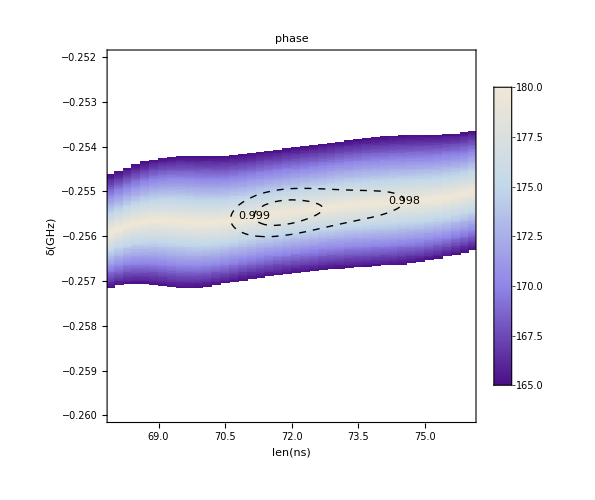

```mathematica
Show[ListDensityPlot[RPhase3,ColorFunction->"LakeColors",Mesh->None,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,8}},LabelStyle->{FontSize->15,FontFamily->"Helvetica"}],Right],PlotRange->{{68,76},{-0.260,-0.252},{165,180}},DataRange->{{59,79},{-0.265,-0.250}},PerformanceGoal->"Quality",FrameLabel->{"len(ns)","δ(GHz)"},LabelStyle->Directive[FontSize->17,FontFamily->"Helvetica"],ImageSize->500,PlotLabel->"phase",InterpolationOrder->0],ListContourPlot[Import["new_fid_26525000002_59_79_02_3x.dat"],PlotRange->{All,{-0.260,-0.252},All},DataRange->{{59,79},{-0.265,-0.250}},ContourShading->None,ContourLabels->All,Contours->{{0.998,{Thick,Dashed,Black}},{0.999,{Thick,Dashed,Black}}}]]
```